```mathematica
Directory[]
```

C:\Users\feelus\Repos\vybory\TICparsed

```mathematica
SetDirectory["C:\\Users\\feelus\\Repos\\vybory\\TICparsed"]
```

C:\Users\feelus\Repos\vybory\TICparsed

```mathematica
filenames=FileNames[];
```

```mathematica
filenames[[1]]
```

adygei-Майкопская городская.txt

```mathematica
file=Import[filenames[[1]]];
```

```mathematica
table1=((StringSplit[#,"\t"]&)/@StringSplit[ file,"\n"])[[Join@@Range@@@{1;;13,15;;22}]]//Transpose;
```

```mathematica
table1[[;;,2;;]]=ToExpression[table1[[;;,2;;]]];
```

```mathematica
SplitName[name_]:=Module[{tmp},
tmp=StringSplit[StringSplit[StringReplace[name,
{"foreign-countries"->"foreign_countries",
"kabardin-balkar"->"kabardin_balkar",
"karachaev-cherkess"->"karachaev_cherkess",
"khantu-mansy"->"khantu_mansy",
"leningrad-reg"->"leningrad_reg",
"mari-el"->"mari_el",
"n_osset-alania"->"n_osset_alania",
"st-petersburg"->"st_petersburg",
"yamal-nenetsk"->"yamal_nenetsk"}
],"."][[1]],"-"];
If[Length[tmp]==2,tmp,
If[Length[tmp]==3,{tmp[[1]],StringJoin[tmp[[2]],"-",tmp[[3]]]},
If[Length[tmp]==4,{tmp[[1]],StringJoin[tmp[[2]],"-",tmp[[3]],"-",tmp[[4]]]},
Throw["more than 3 splits"] 
]
]
]
]
```

```mathematica
regions=SplitName[#][[1]]&/@filenames//Union
```

{adygei,altai_rep,altai_terr,amur,arkhangelsk,astrakhan,bashkortostan,baykonur,belgorod,bryansk,buriat,chechen,chelyabinsk,chukot,chuvash,crimea,dagestan,foreign_countries,ingush,irkutsk,ivanovo,jewish_aut,kabardin_balkar,kaliningrad,kalmyk,kaluga,kamchatka_krai,karachaev_cherkess,karel,kemerovo,khabarovsk,khakas,khantu_mansy,kirov,komi,kostroma,krasnodar,krasnoyarsk,kurgan,kursk,leningrad_reg,lipetsk,magadan,mari_el,mordov,moscow_city,moscow_reg,murmansk,nenetsk,nnov,n_osset_alania,novgorod,novosibirsk,omsk,orel,orenburg,penza,permkrai,primorsk,pskov,rostov,ryazan,sakhalin,samara,saratov,sevastopol,smolensk,stavropol,st_petersburg,sverdlovsk,tambov,tatarstan,tomsk,tula,tver,tyumen,tyva,udmurt,ulyanovsk,vladimir,volgograd,vologod,voronezh,yakut,yamal_nenetsk,yaroslavl,zabkray}

```mathematica
readTable[fname_]:=Module[{subname,table1},
subname=SplitName[fname];
table1=((StringSplit[#,"\t"]&)/@StringSplit[ Import[fname],"\n"])[[Join@@Range@@@{1;;13,15;;22}]];
table1=Join[{ConstantArray[subname[[1]],Length[table1[[1]]]],ConstantArray[subname[[2]],Length[table1[[1]]]]},table1]//Transpose;
table1[[;;,4;;]]=ToExpression[table1[[;;,4;;]]];
table1
]
```

```mathematica
readTable[filenames[[3]]]//TableForm
```

adygei | Тахтамукайская  | "УИК №187" | 1492 | 1507 | 0 | 1441 | 28 | 38 | 28 | 1441 | 2 | 1467 | 0 | 0 | 1 | 31 | 3 | 1430 | 2 | 0 | 0 | 0
adygei | Тахтамукайская  | "УИК №188" | 2146 | 1900 | 0 | 1091 | 201 | 608 | 201 | 1091 | 11 | 1281 | 0 | 0 | 4 | 247 | 16 | 973 | 27 | 3 | 5 | 6
adygei | Тахтамукайская  | "УИК №189" | 2326 | 2250 | 0 | 1494 | 200 | 556 | 200 | 1494 | 16 | 1678 | 0 | 0 | 6 | 298 | 12 | 1335 | 14 | 4 | 5 | 4
adygei | Тахтамукайская  | "УИК №190" | 826 | 780 | 0 | 605 | 8 | 167 | 8 | 605 | 9 | 604 | 0 | 0 | 1 | 71 | 21 | 502 | 2 | 1 | 5 | 1
adygei | Тахтамукайская  | "УИК №191" | 521 | 500 | 0 | 383 | 19 | 98 | 19 | 383 | 4 | 398 | 0 | 0 | 1 | 43 | 20 | 330 | 1 | 1 | 1 | 1
adygei | Тахтамукайская  | "УИК №192" | 288 | 250 | 0 | 228 | 14 | 8 | 14 | 228 | 4 | 238 | 0 | 0 | 1 | 33 | 6 | 194 | 1 | 2 | 0 | 1
adygei | Тахтамукайская  | "УИК №193" | 2682 | 2500 | 0 | 2106 | 16 | 378 | 16 | 2106 | 6 | 2116 | 0 | 0 | 4 | 213 | 38 | 1823 | 12 | 9 | 8 | 9
adygei | Тахтамукайская  | "УИК №194" | 2058 | 1950 | 0 | 1815 | 19 | 116 | 19 | 1815 | 48 | 1786 | 0 | 0 | 5 | 88 | 36 | 1633 | 11 | 4 | 6 | 3
adygei | Тахтамукайская  | "УИК №195" | 1522 | 1450 | 0 | 1281 | 10 | 159 | 10 | 1281 | 17 | 1274 | 0 | 0 | 5 | 156 | 35 | 1050 | 9 | 2 | 11 | 6
adygei | Тахтамукайская  | "УИК №196" | 1819 | 1700 | 0 | 1620 | 11 | 69 | 11 | 1620 | 37 | 1594 | 0 | 0 | 3 | 216 | 35 | 1301 | 9 | 13 | 12 | 5
adygei | Тахтамукайская  | "УИК №197" | 1899 | 1800 | 0 | 1100 | 19 | 681 | 19 | 1100 | 25 | 1094 | 0 | 0 | 6 | 169 | 44 | 839 | 14 | 13 | 6 | 3
adygei | Тахтамукайская  | "УИК №198" | 1627 | 1500 | 0 | 1363 | 11 | 126 | 11 | 1361 | 44 | 1328 | 0 | 0 | 5 | 151 | 44 | 1100 | 9 | 7 | 7 | 5
adygei | Тахтамукайская  | "УИК №199" | 1034 | 1050 | 0 | 839 | 112 | 99 | 112 | 839 | 18 | 933 | 0 | 0 | 2 | 90 | 20 | 805 | 7 | 6 | 1 | 2
adygei | Тахтамукайская  | "УИК №200" | 1484 | 1400 | 0 | 1216 | 61 | 123 | 61 | 1216 | 22 | 1255 | 0 | 0 | 2 | 168 | 24 | 1035 | 13 | 6 | 5 | 2
adygei | Тахтамукайская  | "УИК №201" | 247 | 200 | 0 | 180 | 3 | 17 | 3 | 180 | 3 | 180 | 0 | 0 | 0 | 12 | 14 | 151 | 2 | 0 | 0 | 1
adygei | Тахтамукайская  | "УИК №202" | 383 | 350 | 0 | 319 | 23 | 8 | 23 | 319 | 4 | 338 | 0 | 0 | 1 | 23 | 9 | 299 | 2 | 2 | 1 | 1
adygei | Тахтамукайская  | "УИК №203" | 593 | 650 | 0 | 577 | 16 | 57 | 16 | 577 | 6 | 587 | 0 | 0 | 1 | 36 | 26 | 517 | 2 | 4 | 0 | 1
adygei | Тахтамукайская  | "УИК №204" | 292 | 290 | 0 | 234 | 14 | 42 | 14 | 234 | 3 | 245 | 0 | 0 | 2 | 55 | 6 | 180 | 0 | 0 | 2 | 0
adygei | Тахтамукайская  | "УИК №205" | 1655 | 1500 | 0 | 1323 | 57 | 120 | 57 | 1323 | 2 | 1378 | 0 | 0 | 0 | 5 | 5 | 1350 | 7 | 1 | 8 | 2
adygei | Тахтамукайская  | "УИК №206" | 1785 | 1700 | 0 | 1405 | 11 | 284 | 11 | 1405 | 24 | 1392 | 0 | 0 | 4 | 138 | 42 | 1173 | 12 | 11 | 7 | 5
adygei | Тахтамукайская  | "УИК №207" | 3300 | 2700 | 0 | 1339 | 367 | 994 | 367 | 1339 | 32 | 1674 | 0 | 0 | 9 | 241 | 67 | 1282 | 33 | 16 | 13 | 13
adygei | Тахтамукайская  | "УИК №208" | 1530 | 1400 | 0 | 1206 | 9 | 185 | 9 | 1206 | 8 | 1207 | 0 | 0 | 9 | 108 | 39 | 1025 | 12 | 6 | 5 | 3
adygei | Тахтамукайская  | "УИК №209" | 2898 | 2700 | 0 | 2246 | 86 | 368 | 86 | 2246 | 15 | 2317 | 0 | 0 | 10 | 222 | 83 | 1951 | 22 | 7 | 8 | 14
adygei | Тахтамукайская  | "УИК №210" | 2325 | 2100 | 0 | 1925 | 15 | 160 | 15 | 1925 | 25 | 1915 | 0 | 0 | 4 | 162 | 36 | 1667 | 20 | 12 | 8 | 6
adygei | Тахтамукайская  | "УИК №211" | 2625 | 2400 | 0 | 1970 | 10 | 420 | 10 | 1970 | 21 | 1959 | 0 | 0 | 6 | 211 | 94 | 1596 | 23 | 9 | 5 | 15
adygei | Тахтамукайская  | "УИК №212" | 1311 | 1200 | 0 | 1105 | 6 | 89 | 6 | 1105 | 14 | 1097 | 0 | 0 | 3 | 129 | 88 | 839 | 18 | 10 | 4 | 6
adygei | Тахтамукайская  | "УИК №213" | 1586 | 1500 | 0 | 1284 | 10 | 206 | 10 | 1284 | 7 | 1287 | 0 | 0 | 5 | 115 | 28 | 1109 | 11 | 4 | 8 | 7
adygei | Тахтамукайская  | "УИК №214" | 1857 | 1700 | 0 | 1316 | 28 | 356 | 28 | 1316 | 15 | 1329 | 0 | 0 | 3 | 135 | 34 | 1103 | 13 | 12 | 13 | 16
adygei | Тахтамукайская  | "УИК №215" | 1319 | 1100 | 0 | 873 | 28 | 199 | 28 | 873 | 9 | 892 | 0 | 0 | 5 | 112 | 36 | 704 | 11 | 9 | 11 | 4
adygei | Тахтамукайская  | "УИК №216" | 182 | 178 | 0 | 161 | 2 | 15 | 2 | 161 | 1 | 162 | 0 | 0 | 0 | 16 | 6 | 137 | 1 | 0 | 2 | 0
adygei | Тахтамукайская  | "УИК №217" | 2378 | 2200 | 0 | 2171 | 17 | 12 | 17 | 2171 | 24 | 2164 | 0 | 0 | 8 | 193 | 63 | 1856 | 20 | 8 | 9 | 7
adygei | Тахтамукайская  | "УИК №218" | 1114 | 1050 | 0 | 875 | 50 | 125 | 50 | 875 | 5 | 920 | 0 | 0 | 3 | 106 | 5 | 783 | 11 | 6 | 3 | 3
adygei | Тахтамукайская  | "УИК №219" | 2060 | 1750 | 0 | 1308 | 12 | 430 | 12 | 1308 | 16 | 1304 | 0 | 0 | 8 | 257 | 47 | 935 | 33 | 6 | 11 | 7
adygei | Тахтамукайская  | "УИК №220" | 340 | 300 | 0 | 276 | 20 | 4 | 20 | 276 | 0 | 296 | 0 | 0 | 1 | 27 | 22 | 241 | 2 | 3 | 0 | 0
adygei | Тахтамукайская  | "УИК №221" | 1561 | 1500 | 0 | 1325 | 28 | 147 | 28 | 1325 | 17 | 1336 | 0 | 0 | 4 | 199 | 27 | 1075 | 12 | 9 | 3 | 7
adygei | Тахтамукайская  | "УИК №222" | 1211 | 1200 | 0 | 994 | 68 | 138 | 68 | 994 | 15 | 1047 | 0 | 0 | 3 | 165 | 5 | 859 | 7 | 2 | 0 | 6
adygei | Тахтамукайская  | "УИК №223" | 490 | 470 | 0 | 409 | 26 | 35 | 26 | 409 | 3 | 432 | 0 | 0 | 3 | 87 | 13 | 324 | 1 | 0 | 1 | 3
adygei | Тахтамукайская  | "УИК №224" | 211 | 190 | 0 | 182 | 8 | 0 | 8 | 182 | 0 | 190 | 0 | 0 | 1 | 52 | 4 | 131 | 1 | 0 | 1 | 0
adygei | Тахтамукайская  | "УИК №225" | 292 | 270 | 0 | 253 | 5 | 12 | 5 | 253 | 1 | 257 | 0 | 0 | 1 | 30 | 11 | 209 | 0 | 3 | 2 | 1
adygei | Тахтамукайская  | "УИК №276" | 1840 | 1420 | 0 | 1339 | 7 | 74 | 7 | 1339 | 12 | 1334 | 0 | 0 | 5 | 207 | 60 | 1020 | 23 | 7 | 3 | 9

```mathematica
tables={};
Monitor[
For[i=1,i≤Length[filenames],i++,
AppendTo[tables,readTable[filenames[[i]]]]
],
i
];
table=Join@@tables
```

{{adygei,Майкопская городская,"УИК №115",571,550,0,398,40,112,40,398,11,427,0,0,2,58,14,339,2,3,6,3},{adygei,Майкопская городская,"УИК №116",1706,1700,0,1192,44,464,44,1192,36,1200,0,0,6,163,66,924,14,11,8,8},97665,{zabkray,Ононская,"УИК №2721",127,130,0,92,11,27,11,92,0,103,0,0,1,4,11,86,0,1,0,0}}
 |  |  |  |

```mathematica
table//Length
```

97668

```mathematica
table[[2346]]
```

{amur,рабочего поселка (п,"УИК №2809",1678,1775,0,970,26,779,26,970,15,981,0,0,8,231,113,600,6,15,8,0}

```mathematica
RICname=1;
TICname=2;
UICname=3;
InLists=4;
Early=6;
AtRoomOut=7;
AtHomeOut=8;
AtRoomIn=11;
AtHomeIn=10;
WrongIn=12;
TotalIn=13;
Loosed=14;
Overed=15;
ForBaburin=16;
ForGrudinin=17;
ForZhirinovskiy=18;
ForPutin=19;
ForSobchak=20;
ForSuraikin=21;
ForTitov=22;
ForYavlinskiy=23;
```

```mathematica
For[i=1,i≤Length[table],i++,
If[20<table[[i,InLists]]<30,Print[table[[i]]]]
]
```

{amur,Сковородинского района,"УИК №1826",22,220,0,20,0,200,0,20,0,20,0,0,0,10,0,10,0,0,0,0}

{amur,города Благовещенск,"УИК №3009",26,50,0,26,0,24,0,26,0,26,0,0,0,7,1,18,0,0,0,0}

{arkhangelsk,Архангельск, Южная,"УИК №1013",21,21,0,21,0,0,0,21,1,20,0,0,0,1,4,11,3,0,0,1}

{arkhangelsk,Архангельск, Южная,"УИК №1033",29,29,0,29,0,0,0,29,0,29,0,0,0,6,4,18,0,0,0,1}

{arkhangelsk,Архангельск, Южная,"УИК №1036",28,28,0,28,0,0,0,28,2,26,0,0,1,3,6,16,0,0,0,0}

{bashkortostan,Буздякская,"УИК №1570",23,23,0,20,0,3,0,20,0,20,0,0,0,2,0,18,0,0,0,0}

{buriat,Улан-Удэ, Советская,"УИК №864",29,29,0,29,0,0,0,29,1,28,0,0,0,4,0,23,1,0,0,0}

{buriat,Селенгинская,"УИК №624",29,29,0,28,1,0,1,28,0,29,0,0,0,7,1,21,0,0,0,0}

{buriat,Хоринская,"УИК №871",26,26,0,24,2,0,2,24,0,26,0,0,0,4,1,21,0,0,0,0}

{dagestan,Гумбетовская,"УИК №297",28,28,0,28,0,0,0,28,0,28,0,0,0,1,1,26,0,0,0,0}

{dagestan,Гумбетовская,"УИК №314",28,33,0,28,0,5,0,28,0,28,0,0,0,2,0,26,0,0,0,0}

{dagestan,Унцукульская,"УИК №1491",27,27,0,27,0,0,0,27,0,27,0,0,0,3,0,24,0,0,0,0}

{dagestan,Унцукульская,"УИК №1504",21,21,0,21,0,0,0,21,0,21,0,0,0,0,0,21,0,0,0,0}

{dagestan,Чародинская,"УИК №1840",23,23,0,23,0,0,0,23,0,23,0,0,0,0,0,23,0,0,0,0}

{dagestan,Чародинская,"УИК №1844",21,21,0,18,0,3,0,18,0,18,0,0,0,0,0,18,0,0,0,0}

{dagestan,Чародинская,"УИК №1864",23,23,0,23,0,0,0,23,0,23,0,0,0,2,0,21,0,0,0,0}

{dagestan,Ботлихская,"УИК №162",23,25,0,23,0,2,0,23,0,23,0,0,0,2,0,21,0,0,0,0}

{dagestan,Ботлихская,"УИК №186",24,24,0,21,1,2,1,21,0,22,0,0,0,0,0,22,0,0,0,0}

{dagestan,Рутульская,"УИК №1233",29,33,0,24,0,9,0,24,0,24,0,0,0,2,0,22,0,0,0,0}

{dagestan,Хунзахская,"УИК №1696",24,23,0,20,0,3,0,20,1,19,0,0,0,1,0,18,0,0,0,0}

{dagestan,Гунибская,"УИК №349",24,23,0,23,0,0,0,23,0,23,0,0,0,2,0,21,0,0,0,0}

{dagestan,Курахская,"УИК №844",28,23,0,20,0,3,0,20,1,19,0,0,0,2,0,17,0,0,0,0}

{foreign_countries,все,"УИК №8059",26,62,0,26,0,36,0,26,0,26,0,0,1,5,1,15,2,0,1,1}

{foreign_countries,все,"УИК №8075",26,27,0,26,0,1,0,26,0,26,0,0,0,0,0,25,0,0,0,1}

{foreign_countries,все,"УИК №8328",27,30,0,27,0,3,0,27,1,26,0,0,0,1,0,24,1,0,0,0}

{irkutsk,Казачинско-Ленская,"УИК №856",22,34,0,14,3,17,3,14,0,17,0,0,1,0,4,12,0,0,0,0}

{irkutsk,Киренская,"УИК №913",29,29,0,18,0,11,0,18,0,18,0,0,1,2,0,15,0,0,0,0}

{jewish_aut,Биробиджанская городская,"УИК №35",24,25,0,0,22,3,22,0,0,22,0,0,0,4,2,16,0,0,0,0}

{kaliningrad,Калининград, Московская,"УИК №729",23,23,0,23,0,0,0,23,0,23,0,0,0,3,1,18,1,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №211",24,26,0,24,0,2,0,24,0,24,0,0,0,0,0,24,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №212",24,26,0,24,0,2,0,24,0,24,0,0,0,0,0,23,1,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №213",28,30,0,28,0,2,0,28,0,28,0,0,0,1,0,27,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №214",26,28,0,26,0,2,0,26,0,26,0,0,0,0,0,26,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №224",29,31,0,29,0,2,0,29,0,29,0,0,3,2,5,10,5,1,0,3}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №225",29,31,0,29,0,2,0,29,1,28,0,0,0,1,10,16,1,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №227",21,23,0,19,0,4,0,19,0,19,0,0,1,1,6,10,0,1,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №229",28,30,0,26,0,4,0,26,1,25,0,0,0,6,3,14,1,0,1,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №234",27,29,0,27,0,2,0,27,0,27,0,0,0,3,18,6,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №235",28,30,0,28,0,2,0,28,0,28,0,0,0,6,15,4,3,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №237",29,31,0,29,0,2,0,29,0,29,0,0,1,0,8,19,0,0,1,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №240",27,29,0,27,0,2,0,27,0,27,0,0,0,1,5,19,0,0,1,1}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №242",28,30,0,28,0,2,0,28,0,28,0,0,0,1,4,21,2,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №244",28,30,0,28,0,2,0,28,1,27,0,0,0,4,10,11,2,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №245",28,30,0,23,0,7,0,23,0,23,0,0,0,1,6,16,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №246",27,29,0,27,0,2,0,27,0,27,0,0,0,1,8,14,4,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №247",28,30,0,28,0,2,0,28,0,28,0,0,0,0,7,18,2,0,0,1}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №265",23,25,0,23,0,2,0,23,0,23,0,0,0,3,5,14,1,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №271",27,29,0,20,0,9,0,20,0,20,0,0,0,1,3,12,3,0,0,1}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №280",24,26,0,24,0,2,0,24,0,24,0,0,0,0,0,24,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №286",28,30,0,28,0,2,0,28,0,28,0,0,0,1,0,27,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №302",27,29,0,27,0,2,0,27,0,27,0,0,0,4,3,16,1,1,2,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №307",24,26,0,24,0,2,0,24,0,24,0,0,0,10,2,10,2,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №308",24,26,0,24,0,2,0,24,0,24,0,0,0,2,4,17,0,0,1,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №309",25,27,0,25,0,2,0,25,0,25,0,0,0,2,9,14,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №312",22,24,0,22,0,2,0,22,0,22,0,0,0,3,4,13,0,1,0,1}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №314",21,23,0,21,0,2,0,21,1,20,0,0,0,5,3,11,0,0,1,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №320",24,26,0,24,0,2,0,24,0,24,0,0,1,4,2,17,0,0,0,0}

{kamchatka_krai,Петропавловск-Камчатская городская (судовая),"УИК №324",21,23,0,14,0,9,0,14,0,14,0,0,0,1,2,10,0,1,0,0}

{kemerovo,Ижморская,"УИК №1074",28,30,0,27,0,3,0,27,0,27,0,0,0,0,0,27,0,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №821",25,25,0,25,0,0,0,25,0,25,0,0,0,1,14,9,1,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №822",26,26,0,26,0,0,0,26,4,22,0,0,2,3,3,12,1,1,0,0}

{khabarovsk,Советско-Гаванская,"УИК №823",22,24,0,22,0,2,0,22,0,22,0,0,0,4,6,10,0,1,0,1}

{khabarovsk,Советско-Гаванская,"УИК №825",29,29,0,29,0,0,0,29,0,29,0,0,0,20,2,6,1,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №834",25,25,0,25,0,0,0,25,0,25,0,0,0,0,4,20,0,0,0,1}

{khabarovsk,Советско-Гаванская,"УИК №835",23,23,0,23,0,0,0,23,0,23,0,0,0,2,2,19,0,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №837",24,27,0,24,0,3,0,24,0,24,0,0,0,5,5,13,1,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №848",25,25,0,24,0,1,0,24,0,24,0,0,1,5,5,13,0,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №849",26,26,0,26,0,0,0,26,1,25,0,0,0,4,6,15,0,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №850",28,28,0,28,0,0,0,28,1,27,0,0,0,3,7,15,1,1,0,0}

{khabarovsk,Советско-Гаванская,"УИК №852",27,30,0,27,0,3,0,27,0,27,0,0,0,5,2,19,1,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №853",22,22,0,22,0,0,0,22,0,22,0,0,0,0,4,17,1,0,0,0}

{khabarovsk,Советско-Гаванская,"УИК №870",22,25,0,21,0,4,0,21,0,21,0,0,0,6,8,7,0,0,0,0}

{khabarovsk,Охотская,"УИК №860",28,30,0,28,0,2,0,28,0,28,0,0,0,2,11,14,0,0,0,1}

{komi,Воркутинская городская,"УИК №667",24,26,0,22,0,4,0,22,1,21,0,0,1,0,1,19,0,0,0,0}

{krasnodar,Новороссийск, Судовая,"УИК №3696",24,24,0,24,0,0,0,24,0,24,0,0,0,2,5,17,0,0,0,0}

{krasnodar,Новороссийск, Судовая,"УИК №3699",24,24,0,24,0,0,0,24,1,23,0,0,0,1,2,17,1,0,1,1}

{krasnoyarsk,Новоселовская,"УИК №1757",25,40,0,21,0,19,0,21,0,21,0,0,0,6,0,13,2,0,0,0}

{krasnoyarsk,Новоселовская,"УИК №1761",21,37,0,14,0,23,0,14,0,14,0,0,0,0,2,12,0,0,0,0}

{krasnoyarsk,Бирилюсская,"УИК №933",23,43,0,12,3,28,3,12,0,15,0,0,0,1,0,14,0,0,0,0}

{krasnoyarsk,Богучанская,"УИК №1009",28,30,0,26,0,4,0,26,0,26,0,0,0,0,0,26,0,0,0,0}

{krasnoyarsk,Назаровская,"УИК №1672",24,23,0,17,0,6,0,17,0,17,0,0,0,0,4,13,0,0,0,0}

{krasnoyarsk,Ирбейская,"УИК №1292",28,32,0,10,2,20,2,10,0,12,0,0,0,7,0,5,0,0,0,0}

{krasnoyarsk,Рыбинская,"УИК №1840",29,28,0,24,1,3,1,24,0,25,0,0,0,2,4,18,0,1,0,0}

{krasnoyarsk,Рыбинская,"УИК №1841",25,27,0,24,1,2,1,24,0,25,0,0,0,0,0,25,0,0,0,0}

{krasnoyarsk,Абанская,"УИК №787",26,25,0,16,5,4,5,16,0,21,0,0,0,6,1,14,0,0,0,0}

{krasnoyarsk,Абанская,"УИК №813",26,24,0,20,2,2,2,20,0,22,0,0,0,1,2,19,0,0,0,0}

{krasnoyarsk,Канская,"УИК №1372",23,55,0,23,0,32,0,23,0,23,0,0,0,0,1,22,0,0,0,0}

{krasnoyarsk,Манская,"УИК №1594",21,15,0,9,2,4,2,9,0,11,0,0,0,0,3,8,0,0,0,0}

{kurgan,Частоозерская,"УИК №924",27,40,0,21,4,15,4,21,0,25,0,0,0,1,1,23,0,0,0,0}

{magadan,Магаданская,"УИК №89",23,23,0,23,0,0,0,23,0,23,0,0,0,2,0,21,0,0,0,0}

{magadan,Магаданская,"УИК №92",28,28,0,28,0,0,0,28,0,28,0,0,0,2,0,26,0,0,0,0}

{magadan,Магаданская,"УИК №93",25,25,0,25,0,0,0,25,0,25,0,0,0,2,2,21,0,0,0,0}

{magadan,Магаданская,"УИК №94",24,24,0,24,0,0,0,24,0,24,0,0,0,2,1,21,0,0,0,0}

{magadan,Магаданская,"УИК №95",25,25,0,25,0,0,0,25,0,25,0,0,0,0,0,25,0,0,0,0}

{magadan,Магаданская,"УИК №98",24,26,0,24,0,2,0,24,0,24,0,0,1,1,3,16,2,1,0,0}

{magadan,Магаданская,"УИК №99",24,26,0,24,0,2,0,24,0,24,0,0,0,0,5,15,3,0,0,1}

{magadan,Магаданская,"УИК №100",27,29,0,27,0,2,0,27,0,27,0,0,0,1,5,15,2,2,2,0}

{magadan,Магаданская,"УИК №101",28,30,0,28,0,2,0,28,0,28,0,0,1,6,7,12,1,1,0,0}

{magadan,Магаданская,"УИК №102",28,30,0,28,0,2,0,28,0,28,0,0,0,0,1,27,0,0,0,0}

{magadan,Магаданская,"УИК №104",24,28,0,24,0,4,0,24,0,24,0,0,0,2,2,19,1,0,0,0}

{magadan,Магаданская,"УИК №105",23,23,0,23,0,0,0,23,0,23,0,0,0,0,3,20,0,0,0,0}

{moscow_reg,Коломенская городская,"УИК №1043",28,50,0,28,0,22,0,28,0,28,0,0,0,0,4,22,2,0,0,0}

{murmansk,Мурманская,"УИК №500",28,28,0,27,0,1,0,27,0,27,0,0,0,3,2,19,3,0,0,0}

{murmansk,Мурманская,"УИК №501",22,25,0,22,0,3,0,22,0,22,0,0,1,3,3,11,1,0,3,0}

{murmansk,Мурманская,"УИК №503",26,26,0,26,0,0,0,26,1,25,0,0,0,5,2,18,0,0,0,0}

{murmansk,Мурманская,"УИК №513",28,31,0,26,0,5,0,26,0,26,0,0,0,1,1,21,2,1,0,0}

{murmansk,Мурманская,"УИК №514",27,27,0,27,0,0,0,27,0,27,0,0,0,5,1,21,0,0,0,0}

{murmansk,Мурманская,"УИК №515",26,26,0,24,0,2,0,24,0,24,0,0,0,0,4,18,2,0,0,0}

{murmansk,Мурманская,"УИК №516",27,27,0,27,0,0,0,27,0,27,0,0,0,6,0,20,0,0,1,0}

{murmansk,Мурманская,"УИК №517",27,27,0,27,0,0,0,27,0,27,0,0,0,2,3,21,1,0,0,0}

{murmansk,Мурманская,"УИК №518",24,24,0,24,0,0,0,24,0,24,0,0,0,3,4,17,0,0,0,0}

{murmansk,Мурманская,"УИК №522",28,28,0,28,0,0,0,28,0,28,0,0,0,2,6,18,2,0,0,0}

{murmansk,Мурманская,"УИК №524",25,25,0,25,0,0,0,25,0,25,0,0,0,1,2,20,1,0,0,1}

{murmansk,Мурманская,"УИК №530",25,25,0,25,0,0,0,25,1,24,0,0,1,0,3,20,0,0,0,0}

{murmansk,Мурманская,"УИК №531",21,21,0,21,0,0,0,21,0,21,0,0,0,1,1,17,0,0,1,1}

{murmansk,Мурманская,"УИК №532",23,24,0,23,0,1,0,23,0,23,0,0,0,2,2,18,0,0,1,0}

{murmansk,Мурманская,"УИК №534",26,30,0,23,0,7,0,23,0,23,0,0,0,7,1,15,0,0,0,0}

{murmansk,Мурманская,"УИК №535",27,27,0,27,0,0,0,27,1,26,0,0,0,2,3,13,4,2,1,1}

{murmansk,Мурманская,"УИК №536",27,28,0,27,0,1,0,27,0,27,0,0,0,4,2,18,2,0,0,1}

{murmansk,Мурманская,"УИК №547",22,23,0,22,0,1,0,22,0,22,0,0,1,0,2,19,0,0,0,0}

{murmansk,Мурманская,"УИК №551",21,21,0,20,0,1,0,20,0,20,0,0,0,2,3,14,0,0,0,1}

{murmansk,Мурманская,"УИК №554",21,21,0,19,0,2,0,19,0,19,0,0,0,2,3,7,3,1,0,3}

{murmansk,Мурманская,"УИК №557",21,21,0,21,0,0,0,21,0,21,0,0,1,1,4,15,0,0,0,0}

{murmansk,Мурманская,"УИК №562",21,21,0,17,0,4,0,17,0,17,0,0,0,0,5,11,1,0,0,0}

{murmansk,Мурманская,"УИК №566",26,26,0,26,0,0,0,26,2,24,0,0,2,2,2,14,1,0,1,2}

{murmansk,Мурманская,"УИК №567",23,23,0,23,0,0,0,23,0,23,0,0,0,3,1,14,1,1,1,2}

{murmansk,Мурманская,"УИК №571",28,28,0,25,0,3,0,25,0,25,0,0,0,5,4,16,0,0,0,0}

{murmansk,Мурманская,"УИК №576",25,25,0,25,0,0,0,25,0,25,0,0,0,0,0,24,0,0,0,1}

{murmansk,Мурманская,"УИК №599",25,28,0,25,0,3,0,25,1,24,0,0,0,1,2,19,1,0,0,1}

{murmansk,Мурманская,"УИК №617",29,32,0,29,0,3,0,29,0,29,0,0,0,3,7,17,1,0,0,1}

{murmansk,Мурманская,"УИК №619",27,27,0,27,0,0,0,27,0,27,0,0,0,0,1,23,2,1,0,0}

{murmansk,Мурманская,"УИК №621",28,28,0,28,0,0,0,28,0,28,0,0,0,2,1,19,5,1,0,0}

{murmansk,Мурманская,"УИК №622",28,28,0,28,0,0,0,28,0,28,0,0,1,2,3,21,1,0,0,0}

{murmansk,Мурманская,"УИК №623",29,30,0,29,0,1,0,29,0,29,0,0,1,4,5,17,1,0,1,0}

{murmansk,Мурманская,"УИК №624",27,27,0,27,0,0,0,27,0,27,0,0,0,1,3,23,0,0,0,0}

{murmansk,Мурманская,"УИК №625",29,29,0,29,0,0,0,29,0,29,0,0,1,5,2,19,0,1,1,0}

{murmansk,Мурманская,"УИК №626",25,25,0,25,0,0,0,25,0,25,0,0,0,3,2,19,1,0,0,0}

{murmansk,Мурманская,"УИК №627",26,26,0,26,0,0,0,26,0,26,0,0,1,2,1,18,4,0,0,0}

{murmansk,Мурманская,"УИК №628",27,27,0,27,0,0,0,27,0,27,0,0,0,3,4,15,0,2,2,1}

{murmansk,Мурманская,"УИК №630",28,28,0,28,0,0,0,28,0,28,0,0,0,3,6,17,2,0,0,0}

{murmansk,Мурманская,"УИК №646",29,29,0,29,0,0,0,29,1,28,0,0,1,7,1,16,1,1,0,1}

{murmansk,Мурманская,"УИК №663",28,28,0,28,0,0,0,28,1,27,0,0,0,0,1,21,2,0,1,2}

{murmansk,Мурманская,"УИК №664",28,28,0,28,0,0,0,28,0,28,0,0,0,2,1,22,3,0,0,0}

{murmansk,Мурманская,"УИК №669",29,30,0,29,0,1,0,29,0,29,0,0,0,3,3,22,1,0,0,0}

{omsk,Муромцевская,"УИК №1099",27,33,0,23,0,10,0,23,0,23,0,0,0,2,1,20,0,0,0,0}

{orenburg,Домбаровская,"УИК №468",24,50,0,20,0,30,0,20,0,20,0,0,0,0,1,19,0,0,0,0}

{orenburg,Домбаровская,"УИК №471",27,33,0,22,0,11,0,22,0,22,0,0,0,9,2,11,0,0,0,0}

{orenburg,Илекская,"УИК №508",27,54,0,24,1,29,1,24,0,25,0,0,1,4,1,18,0,1,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5801",26,26,0,26,0,0,0,26,0,26,0,0,0,6,3,15,1,1,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5802",22,22,0,22,0,0,0,22,0,22,0,0,3,3,3,12,1,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5804",22,22,0,22,0,0,0,22,0,22,0,0,0,6,1,14,0,1,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5810",22,22,0,22,0,0,0,22,0,22,0,0,1,1,4,16,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5827",22,22,0,22,0,0,0,22,0,22,0,0,0,1,6,12,2,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5829",26,26,0,26,0,0,0,26,0,26,0,0,0,1,6,17,1,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5830",28,28,0,25,0,3,0,25,0,25,0,0,0,2,5,17,0,0,1,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5835",29,29,0,29,0,0,0,29,3,26,0,0,0,6,4,16,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5837",23,23,0,23,0,0,0,23,0,23,0,0,0,8,2,12,0,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5838",23,23,0,21,0,2,0,21,0,21,0,0,1,5,4,10,1,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5839",22,22,0,19,0,3,0,19,0,19,0,0,0,4,4,10,0,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5844",29,29,0,29,0,0,0,29,0,29,0,0,0,0,0,29,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5847",23,23,0,23,0,0,0,23,0,23,0,0,0,2,5,16,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5848",21,21,0,21,0,0,0,21,0,21,0,0,0,8,1,11,1,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5849",21,21,0,21,0,0,0,21,0,21,0,0,0,1,8,9,2,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5850",21,21,0,21,0,0,0,21,1,20,0,0,0,0,2,17,0,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5851",21,21,0,21,0,0,0,21,0,21,0,0,0,2,2,15,2,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5855",27,27,0,27,0,0,0,27,0,27,0,0,0,2,5,20,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5856",24,24,0,24,0,0,0,24,0,24,0,0,1,0,2,21,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5857",26,26,0,26,0,0,0,26,0,26,0,0,0,0,0,26,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5858",26,26,0,26,0,0,0,26,0,26,0,0,0,0,0,26,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5859",26,26,0,26,0,0,0,26,0,26,0,0,0,0,2,24,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5862",28,28,0,28,0,0,0,28,1,27,0,0,0,4,5,17,0,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5865",27,27,0,27,0,0,0,27,1,26,0,0,0,5,4,14,1,0,2,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5866",26,26,0,26,0,0,0,26,0,26,0,0,1,1,4,18,2,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5867",28,28,0,28,0,0,0,28,1,27,0,0,0,3,6,13,3,2,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5868",26,26,0,26,0,0,0,26,0,26,0,0,0,5,8,10,1,1,1,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5869",26,26,0,26,0,0,0,26,0,26,0,0,0,2,3,21,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5870",27,27,0,27,0,0,0,27,0,27,0,0,0,1,2,23,0,0,1,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5871",27,27,0,27,0,0,0,27,0,27,0,0,0,0,1,26,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5872",29,29,0,29,0,0,0,29,0,29,0,0,1,0,1,26,1,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5873",27,27,0,27,0,0,0,27,0,27,0,0,0,1,0,26,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5877",28,28,0,28,0,0,0,28,0,28,0,0,0,1,1,26,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5884",23,23,0,23,0,0,0,23,0,23,0,0,1,1,6,15,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5885",24,24,0,24,0,0,0,24,0,24,0,0,1,2,5,15,0,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5886",24,24,0,24,0,0,0,24,0,24,0,0,1,0,2,20,0,1,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5887",27,27,0,27,0,0,0,27,0,27,0,0,0,0,2,25,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5888",22,22,0,22,0,0,0,22,1,21,0,0,0,3,3,15,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5889",29,29,0,29,0,0,0,29,0,29,0,0,0,1,7,19,1,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5890",27,27,0,27,0,0,0,27,0,27,0,0,0,14,8,3,0,0,2,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5899",23,23,0,23,0,0,0,23,1,22,0,0,1,2,1,16,1,1,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5901",23,23,0,23,0,0,0,23,0,23,0,0,0,16,4,3,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5902",23,23,0,23,0,0,0,23,0,23,0,0,0,0,0,23,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5903",22,22,0,22,0,0,0,22,0,22,0,0,0,6,5,11,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5913",23,24,0,23,0,1,0,23,0,23,0,0,0,18,4,1,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5921",21,21,0,21,0,0,0,21,0,21,0,0,0,8,4,8,0,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5922",23,23,0,23,0,0,0,23,0,23,0,0,0,1,2,20,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5923",25,25,0,25,0,0,0,25,0,25,0,0,0,3,12,7,2,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5925",23,23,0,23,0,0,0,23,0,23,0,0,2,7,1,12,0,1,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5926",23,23,0,23,0,0,0,23,0,23,0,0,0,0,0,23,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5927",21,21,0,21,0,0,0,21,0,21,0,0,0,1,2,16,2,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5928",24,24,0,24,0,0,0,24,0,24,0,0,1,0,3,20,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5929",28,28,0,28,0,0,0,28,0,28,0,0,0,3,5,19,0,0,0,1}

{primorsk,Владивосток, Фрунзенская,"УИК №5930",29,29,0,29,0,0,0,29,0,29,0,0,0,11,7,11,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5933",21,21,0,21,0,0,0,21,0,21,0,0,0,7,3,10,1,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5934",22,22,0,22,0,0,0,22,0,22,0,0,0,7,0,15,0,0,0,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5942",26,26,0,26,0,0,0,26,0,26,0,0,0,1,4,19,0,0,0,2}

{primorsk,Владивосток, Фрунзенская,"УИК №5944",28,29,0,28,0,1,0,28,0,28,0,0,1,0,4,22,0,0,1,0}

{primorsk,Владивосток, Фрунзенская,"УИК №5946",22,22,0,22,0,0,0,22,0,22,0,0,0,4,6,11,0,0,0,1}

{primorsk,Находкинская городская,"УИК №7112",28,28,0,28,0,0,0,28,0,28,0,0,0,4,9,14,0,1,0,0}

{primorsk,Находкинская городская,"УИК №7113",21,21,0,21,0,0,0,21,0,21,0,0,0,1,1,19,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7119",28,28,0,28,0,0,0,28,0,28,0,0,0,2,3,19,1,1,0,2}

{primorsk,Находкинская городская,"УИК №7120",29,29,0,29,0,0,0,29,0,29,0,0,0,1,4,24,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7121",25,25,0,25,0,0,0,25,0,25,0,0,0,2,15,5,3,0,0,0}

{primorsk,Находкинская городская,"УИК №7122",25,25,0,25,0,0,0,25,1,24,0,0,0,5,2,16,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7124",25,25,0,25,0,0,0,25,0,25,0,0,0,3,4,17,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7125",29,29,0,29,0,0,0,29,0,29,0,0,0,1,4,24,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7126",29,29,0,29,0,0,0,29,1,28,0,0,0,0,3,24,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7127",29,29,0,29,0,0,0,29,0,29,0,0,0,1,7,21,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7128",28,28,0,28,0,0,0,28,0,28,0,0,0,0,3,23,0,2,0,0}

{primorsk,Находкинская городская,"УИК №7129",29,29,0,29,0,0,0,29,0,29,0,0,0,0,2,27,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7130",29,29,0,28,0,1,0,28,0,28,0,0,0,1,4,22,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7132",27,27,0,27,0,0,0,27,1,26,0,0,0,1,4,15,4,1,1,0}

{primorsk,Находкинская городская,"УИК №7134",24,24,0,24,0,0,0,24,0,24,0,0,0,3,3,17,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7135",23,23,0,23,0,0,0,23,0,23,0,0,0,3,2,17,0,0,1,0}

{primorsk,Находкинская городская,"УИК №7137",21,23,0,21,0,2,0,21,0,21,0,0,0,3,3,15,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7138",23,25,0,23,0,2,0,23,0,23,0,0,0,2,3,17,0,0,1,0}

{primorsk,Находкинская городская,"УИК №7139",23,25,0,23,0,2,0,23,0,23,0,0,0,2,2,19,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7141",29,31,0,28,0,3,0,28,0,28,0,0,0,2,6,19,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7144",23,25,0,23,0,2,0,23,0,23,0,0,0,0,0,23,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7147",29,29,0,29,0,0,0,29,0,29,0,0,0,0,0,29,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7148",29,29,0,29,0,0,0,29,0,29,0,0,0,1,0,28,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7149",29,29,0,29,0,0,0,29,0,29,0,0,0,0,0,29,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7150",29,29,0,29,0,0,0,29,0,29,0,0,0,0,1,28,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7151",22,22,0,22,0,0,0,22,0,22,0,0,0,0,3,18,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7153",23,23,0,23,0,0,0,23,0,23,0,0,0,0,0,23,0,0,0,0}

{primorsk,Находкинская городская,"УИК №7154",29,29,0,29,0,0,0,29,2,27,0,0,0,3,7,14,2,0,0,1}

{primorsk,Находкинская городская,"УИК №7171",29,29,0,29,0,0,0,29,0,29,0,0,1,1,11,11,2,1,0,2}

{primorsk,Находкинская городская,"УИК №7174",28,28,0,28,0,0,0,28,0,28,0,0,0,0,27,0,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7176",28,28,0,28,0,0,0,28,1,27,0,0,0,2,2,22,0,1,0,0}

{primorsk,Находкинская городская,"УИК №7177",24,24,0,24,0,0,0,24,0,24,0,0,1,5,3,12,1,0,0,2}

{primorsk,Находкинская городская,"УИК №7178",29,29,0,29,0,0,0,29,0,29,0,0,1,4,4,17,2,0,1,0}

{primorsk,Находкинская городская,"УИК №7181",21,21,0,21,0,0,0,21,0,21,0,0,1,4,3,12,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7185",25,25,0,25,0,0,0,25,0,25,0,0,0,2,10,12,1,0,0,0}

{primorsk,Находкинская городская,"УИК №7186",22,22,0,22,0,0,0,22,0,22,0,0,1,3,6,8,3,0,0,1}

{ryazan,Шацкая,"УИК №763",25,26,0,22,3,1,3,22,0,25,0,0,0,0,1,24,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №555",24,24,0,24,0,0,0,24,0,24,0,0,1,6,7,8,0,1,1,0}

{sakhalin,Невельская судовая,"УИК №556",26,26,0,26,0,0,0,26,0,26,0,0,0,0,7,19,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №557",22,22,0,22,0,0,0,22,0,22,0,0,0,10,5,5,2,0,0,0}

{sakhalin,Невельская судовая,"УИК №559",24,24,0,24,0,0,0,24,0,24,0,0,0,0,4,18,1,0,0,1}

{sakhalin,Невельская судовая,"УИК №561",21,21,0,21,0,0,0,21,0,21,0,0,1,7,1,11,0,1,0,0}

{sakhalin,Невельская судовая,"УИК №584",26,26,0,26,0,0,0,26,0,26,0,0,0,2,2,21,0,1,0,0}

{sakhalin,Невельская судовая,"УИК №585",24,24,0,24,0,0,0,24,0,24,0,0,0,0,3,19,1,1,0,0}

{sakhalin,Невельская судовая,"УИК №586",24,24,0,24,0,0,0,24,0,24,0,0,0,0,0,24,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №591",28,28,0,28,0,0,0,28,0,28,0,0,0,3,13,9,3,0,0,0}

{sakhalin,Невельская судовая,"УИК №592",26,26,0,26,0,0,0,26,0,26,0,0,0,2,3,19,1,0,0,1}

{sakhalin,Невельская судовая,"УИК №606",26,26,0,26,0,0,0,26,0,26,0,0,0,4,7,12,3,0,0,0}

{sakhalin,Невельская судовая,"УИК №623",27,27,0,27,0,0,0,27,0,27,0,0,0,0,0,27,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №625",29,29,0,29,0,0,0,29,0,29,0,0,0,6,2,18,1,2,0,0}

{sakhalin,Невельская судовая,"УИК №626",24,24,0,24,0,0,0,24,0,24,0,0,0,2,2,17,3,0,0,0}

{sakhalin,Невельская судовая,"УИК №627",23,23,0,23,0,0,0,23,0,23,0,0,0,0,0,23,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №629",21,21,0,21,0,0,0,21,0,21,0,0,0,14,5,2,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №630",24,24,0,24,0,0,0,24,0,24,0,0,0,2,9,13,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №632",22,22,0,22,0,0,0,22,5,17,0,0,0,2,2,13,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №637",28,28,0,28,0,0,0,28,1,27,0,0,0,0,1,25,0,0,1,0}

{sakhalin,Невельская судовая,"УИК №639",24,24,0,24,0,0,0,24,0,24,0,0,0,3,3,16,2,0,0,0}

{sakhalin,Невельская судовая,"УИК №640",24,24,0,24,0,0,0,24,0,24,0,0,1,0,4,18,1,0,0,0}

{sakhalin,Невельская судовая,"УИК №641",25,25,0,25,0,0,0,25,0,25,0,0,0,4,7,13,0,0,1,0}

{sakhalin,Невельская судовая,"УИК №642",23,23,0,23,0,0,0,23,0,23,0,0,0,0,0,23,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №643",24,24,0,24,0,0,0,24,0,24,0,0,0,7,2,14,1,0,0,0}

{sakhalin,Невельская судовая,"УИК №644",24,24,0,24,0,0,0,24,0,24,0,0,0,3,1,12,0,0,7,1}

{sakhalin,Невельская судовая,"УИК №645",23,23,0,23,0,0,0,23,0,23,0,0,0,7,3,13,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №648",25,25,0,25,0,0,0,25,0,25,0,0,0,0,0,25,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №650",21,21,0,19,0,2,0,19,0,19,0,0,0,0,4,14,0,1,0,0}

{sakhalin,Невельская судовая,"УИК №655",27,27,0,27,0,0,0,27,0,27,0,0,0,2,4,21,0,0,0,0}

{sakhalin,Невельская судовая,"УИК №656",22,22,0,22,0,0,0,22,0,22,0,0,0,2,1,16,2,0,1,0}

{sakhalin,Холмская судовая,"УИК №432",23,23,0,22,0,1,0,22,0,22,0,0,0,1,2,19,0,0,0,0}

{sakhalin,Холмская судовая,"УИК №440",27,27,0,27,0,0,0,27,0,27,0,0,0,3,3,17,2,0,1,1}

{sakhalin,Корсаковская,"УИК №741",21,21,0,21,0,0,0,21,0,21,0,0,0,3,1,16,1,0,0,0}

{sakhalin,Корсаковская,"УИК №747",22,22,0,22,0,0,0,22,2,20,0,0,2,5,3,8,1,1,0,0}

{sakhalin,Корсаковская,"УИК №748",24,24,0,24,0,0,0,24,0,24,0,0,0,6,3,14,1,0,0,0}

{sakhalin,Корсаковская,"УИК №756",23,23,0,23,0,0,0,23,0,23,0,0,1,2,4,14,1,0,1,0}

{sakhalin,Корсаковская,"УИК №758",25,25,0,25,0,0,0,25,0,25,0,0,0,0,3,18,0,1,1,2}

{sakhalin,Корсаковская,"УИК №759",23,23,0,23,0,0,0,23,0,23,0,0,0,4,5,10,2,1,1,0}

{sakhalin,Корсаковская,"УИК №761",25,25,0,25,0,0,0,25,0,25,0,0,1,2,3,16,3,0,0,0}

{sakhalin,Корсаковская,"УИК №762",24,24,0,24,0,0,0,24,0,24,0,0,0,2,5,15,2,0,0,0}

{sakhalin,Корсаковская,"УИК №764",22,22,0,22,0,0,0,22,0,22,0,0,1,3,5,12,0,1,0,0}

{st_petersburg,Территориальная избирательная комиссия №2,"УИК №188",25,25,25,0,0,0,25,0,2,23,0,0,1,4,3,10,4,0,0,1}

{st_petersburg,Территориальная избирательная комиссия №2,"УИК №192",21,21,21,0,0,0,21,0,0,21,0,0,0,5,1,13,1,1,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №700",25,25,25,0,0,0,25,0,1,24,0,0,0,5,6,9,2,0,1,1}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №701",25,25,25,0,0,0,25,0,0,25,0,0,0,2,3,18,1,0,1,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №702",21,21,21,0,0,0,21,0,0,21,0,0,0,5,2,14,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №704",21,21,21,0,0,0,21,0,0,21,0,0,0,7,1,13,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №708",21,21,0,21,0,0,0,21,0,21,0,0,0,4,1,16,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №709",28,28,28,0,0,0,28,0,0,28,0,0,0,7,3,15,2,0,0,1}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №711",22,22,22,0,0,0,22,0,0,22,0,0,0,5,3,14,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №714",26,26,26,0,0,0,26,0,2,24,0,0,0,6,1,15,0,1,0,1}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №715",26,26,26,0,0,0,26,0,0,26,0,0,0,1,0,23,0,0,1,1}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №716",25,30,24,0,0,6,24,0,0,24,0,0,0,1,2,20,0,0,1,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №717",25,25,25,0,0,0,25,0,0,25,0,0,0,4,0,20,1,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №718",25,25,25,0,0,0,25,0,0,25,0,0,0,2,4,19,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №720",29,29,0,29,0,0,0,29,0,29,0,0,0,0,2,21,3,1,1,1}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №721",29,29,0,24,0,5,0,24,0,24,0,0,0,2,1,20,0,0,1,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №722",28,28,0,28,0,0,0,28,0,28,0,0,0,0,2,25,1,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №725",25,25,25,0,0,0,25,0,0,25,0,0,0,2,2,18,1,0,0,2}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №726",25,25,24,0,0,1,24,0,0,24,0,0,0,2,4,18,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №727",25,25,25,0,0,0,25,0,0,25,0,0,0,4,3,16,0,0,1,1}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №739",24,24,24,0,0,0,24,0,0,24,0,0,0,1,3,19,1,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №740",27,27,27,0,0,0,27,0,0,27,0,0,0,1,9,14,3,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №741",24,24,24,0,0,0,24,0,0,24,0,0,0,2,2,15,1,0,0,4}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №742",27,27,27,0,0,0,27,0,0,27,0,0,0,2,11,14,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №743",26,26,26,0,0,0,26,0,1,25,0,0,1,4,7,12,0,0,0,1}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №755",27,30,0,27,0,3,0,27,2,25,0,0,1,4,4,16,0,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №756",25,25,0,25,0,0,0,25,0,25,0,0,2,4,2,16,1,0,0,0}

{st_petersburg,Территориальная избирательная комиссия №3,"УИК №2299",28,28,0,28,0,0,0,28,1,27,0,0,1,7,3,16,0,0,0,0}

{sverdlovsk,Гаринская,"УИК №338",28,30,0,17,3,10,3,17,0,20,0,0,0,0,7,13,0,0,0,0}

{vologod,Череповецкая городская,"УИК №1017",21,21,0,21,0,0,0,21,0,21,0,0,0,5,2,13,0,1,0,0}

{voronezh,Рамонская,"УИК №3231",21,80,0,21,0,59,0,21,0,21,0,0,0,5,0,16,0,0,0,0}

{yakut,Верхневилюйская,"УИК №97",27,35,0,23,0,12,0,23,0,23,0,0,0,11,0,12,0,0,0,0}

{yakut,Усть-Алданская,"УИК №597",24,20,0,18,0,2,0,18,0,18,0,0,0,7,0,11,0,0,0,0}

{zabkray,Тунгокоченская,"УИК №3208",26,35,0,17,0,18,0,17,0,17,0,0,0,0,5,12,0,0,0,0}

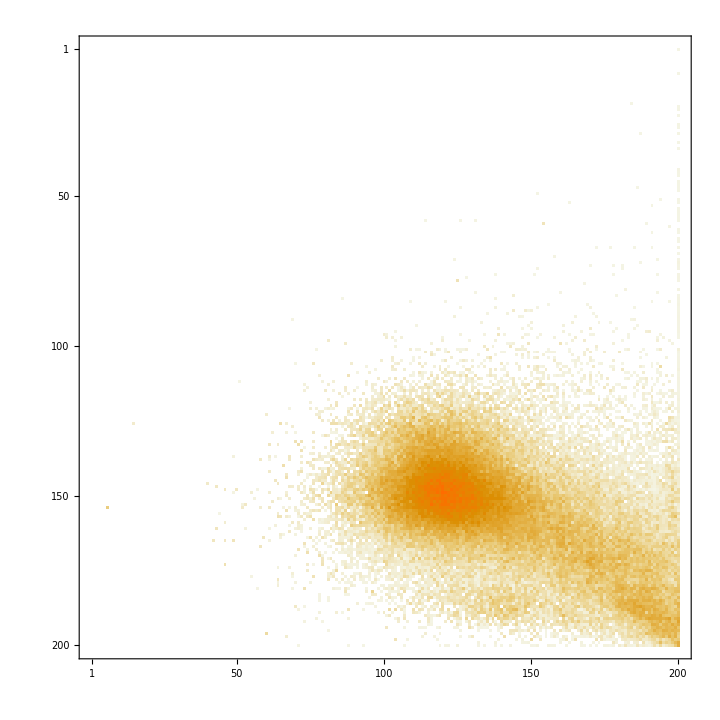

```mathematica
size=200;
turnoutCandidate=ConstantArray[ConstantArray[0,size],size];
forCandidate=ForPutin;
For[i=1,i≤Length[table],i++,
If[table[[i,InLists]]==0||table[[i,TotalIn]]==0,1(*Print[table[[i]]]*),
If[(*table[[i,RICname]]!="crimea"
&&table[[i,RICname]]!="sevastopol"*)
True||table[[i,RICname]]!="foreign_countries"
,
turnout=Floor[table[[i,TotalIn]]/table[[i,InLists]]*size]+1;
candidate=Floor[table[[i,forCandidate]]/table[[i,TotalIn]]*size]+1;
If[turnout==size+1,turnout=size];
If[candidate==size+1,candidate=size];
If[1≤candidate≤size&&1≤candidate≤size,
turnoutCandidate[[candidate,turnout]]+=table[[i,InLists]],
Print[table[[i]]]
]
]
]
];
MatrixPlot[turnoutCandidate]
```

```mathematica
Max[turnoutCandidate]
```

558644

```mathematica
turnoutCandidate[[100,100]]
```

68775

```mathematica
Monitor[
For[j=1,j≤Length[regions],j++,
turnoutCandidate=ConstantArray[ConstantArray[0,100],100];
forCandidate=ForPutin;
For[i=1,i≤Length[table],i++,
If[table[[i,InLists]]==0||table[[i,TotalIn]]==0,1(*Print[table[[i]]]*),
If[table[[i,RICname]]==regions[[j]],
turnout=Floor[table[[i,TotalIn]]/table[[i,InLists]]*100]+1;
candidate=Floor[table[[i,forCandidate]]/table[[i,TotalIn]]*100]+1;
If[turnout==101,turnout=100];
If[candidate==101,candidate=100];
If[1≤candidate≤100&&1≤candidate≤100,
turnoutCandidate[[candidate,turnout]]+=table[[i,InLists]],
Print[table[[i]]]
]
]
]
];
Export["..\\images\\1\\"<>regions[[j]]<>".png",MatrixPlot[turnoutCandidate]]
],
regions[[j]]
]
```

```mathematica
regions//TableForm
```

adygei
altai_rep
altai_terr
amur
arkhangelsk
astrakhan
bashkortostan
baykonur
belgorod
bryansk
buriat
chechen
chelyabinsk
chukot
chuvash
crimea
dagestan
foreign_countries
ingush
irkutsk
ivanovo
jewish_aut
kabardin_balkar
kaliningrad
kalmyk
kaluga
kamchatka_krai
karachaev_cherkess
karel
kemerovo
khabarovsk
khakas
khantu_mansy
kirov
komi
kostroma
krasnodar
krasnoyarsk
kurgan
kursk
leningrad_reg
lipetsk
magadan
mari_el
mordov
moscow_city
moscow_reg
murmansk
nenetsk
nnov
n_osset_alania
novgorod
novosibirsk
omsk
orel
orenburg
penza
permkrai
primorsk
pskov
rostov
ryazan
sakhalin
samara
saratov
sevastopol
smolensk
stavropol
st_petersburg
sverdlovsk
tambov
tatarstan
tomsk
tula
tver
tyumen
tyva
udmurt
ulyanovsk
vladimir
volgograd
vologod
voronezh
yakut
yamal_nenetsk
yaroslavl
zabkray

```mathematica
Max[turnoutCandidate]
```

8

```mathematica
turnoutCandidate[[100,100]]
```

5

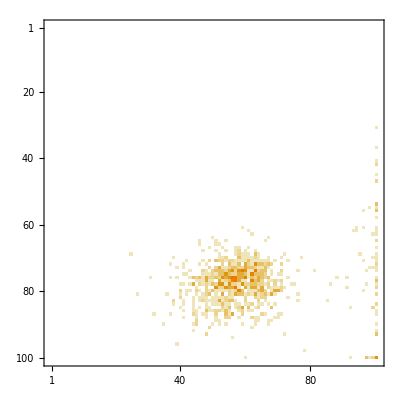

```mathematica
MatrixPlot[turnoutCandidate]
```

```mathematica
Export["..\\images\\arkhangelsk.png",MatrixPlot[turnoutCandidate]]
```

..\images\arkhangelsk.png

```mathematica
Floor[3/2]
```

1

```mathematica
i=5;
Floor[table[[i,TotalIn]]/table[[i,InLists]]*100]+1
```

56

```mathematica
table[[5,TotalIn]]
```

1188

```mathematica
ChurovSaw=ConstantArray[0,100];
forCandidate
For[i=1,i≤Length[table],i++,
If[table[[i,InLists]]==0||table[[i,TotalIn]]==0,1(*Print[table[[i]]]*),
If[table[[i,RICname]]==regions[[j]],
candidate=Floor[table[[i,forCandidate]]/table[[i,TotalIn]]*100]+1;
If[candidate==101,candidate=100, Print[]];
If[1≤candidate≤100&&1≤candidate≤100,
turnoutCandidate[[candidate,turnout]]++,
Print[table[[i]]]
]
]
]
];
```